```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\adiso\Documents\Research\SourceFactors\MathematicaNB

```mathematica
Needs["KerrMSTNu`"]
```

Defining Functions

```mathematica
PhaseCorrectTrans[a_,s_,m_,omega_]:=Module[{ϵ,κ,τ,ϵp},
ϵ = 2*omega;
κ=Sqrt[1-a^2];
τ = (ϵ - m*a)/κ;
ϵp = (ϵ+τ)/2;
2^(-2s)*Exp[-I*κ*ϵp+I*ϵp Log[κ](1-κ)/(1+κ)]
]
PhaseCorrectRef[a_,s_,omega_]:=Module[{ϵ,κ,τ},
ϵ = 2*omega;
κ=Sqrt[1-a^2];
2^(-1-2s)*Exp[I*(1-κ)ϵ/2]
]
PhaseCorrectInc[a_,omega_]:=Module[{ϵ,κ,τ,ϵp},
ϵ = 2*omega;
κ=Sqrt[1-a^2];
Exp[-I*(1-κ)*ϵ/2]/2
]
```

```mathematica
ωshift[ω_]:=ω+ShiftValue
```

```mathematica
derivAin[AinShifted_,Ain_]:=(AinShifted-Ain)/ShiftValue;
```

```mathematica
ExcitationFactorZB[χ_,ω_,ωShift_,ν_,νShift_]:=Module[{Alms,λ,AlmsShift,λShift,BInc,BRef,BIncShift,PhaseInc,PhaseRef},
Alms=sAlm[χ,-2,2,2,ω][[1]];
λ=λTeuk[χ,2,ω,Alms];
AlmsShift=sAlm[χ,-2,2,2,ωShift][[1]];
λShift=λTeuk[χ,2,ωShift,AlmsShift];
BInc=Binc[ν,χ,-2,2,ω,λ];
BRef=Bref[ν,χ,-2,2,ω,λ];
BIncShift=Binc[νShift,χ,-2,2,ωShift,λShift];
PhaseInc=PhaseCorrectInc[χ,ω];
PhaseRef=PhaseCorrectRef[χ,-2,ω];
BRef*PhaseRef/(PhaseInc*2*ω*derivAin[BIncShift,BInc])]
```

```mathematica
ExcitationFactorO[χ_,ω_,ωShift_,ν_,νShift_]:=ExcitationFactorZB[χ,ω,ωShift,ν,νShift]/(Exp[2I*ω*aVals[χ]]*(2ω)^2)
```

```mathematica
spins=ToExpression[StringReplace[Import["Values//All_Spins.txt"],{"["->"{","]"->"}"}]];
```

```mathematica
freq=ToExpression[StringReplace[Import["Values//all_qnm_freq.txt"],{"["->"{","]"->"}"}]];
allω=ToExpression[freq];
```

```mathematica
aVals =Interpolation[{{0.3,0.146100},{0.4,0.262800},{0.5,0.424605},{0.6,0.649046},{0.7,0.962042},{0.8,1.424616},{0.9,2.227500},{0.99,4.778240}}];
```

```mathematica
NuVals=Import["Values//NuValues.mx"];
```

```mathematica
ShiftValue=10^(-9);
χ=spins[[1]]
ω=allω[[1,1]]
```

0.686462

0.526704-0.0812884 ⅈ

```mathematica
GiveNu[χ_,ω_,νS_]:=FindNu[χ,-2,2,ω,λTeuk[χ,2,ω,sAlm[χ,-2,2,2,ω][[1]]],νS][[1]]
```

```mathematica
GiveNu[χ,ω,0.7175+0.417 ⅈ]
```

0.717577+0.417148 ⅈ

```mathematica
Conjugate[0.7175765843237353+0.4171479052241167 ⅈ]
```

0.717577-0.417148 ⅈ

```mathematica
?FindNu
```

```mathematica
χ=0.8
ω=(1.172034−0.151259I)/2
```

0.8

0.586017-0.0756295 ⅈ

```mathematica
FindNu[χ,-2,2,ω,my]
```

{2.58529+0.205297 ⅈ,-2.28983×10^-16-3.64292×10^-17 ⅈ}

```mathematica
sAlmExpansion[χ,-2,2,2,ω/2]
```

2.58529+0.205297 ⅈ

```mathematica
theSPIN=spins[[1]]
theFREQ=allω[[1,1;;8]]
```

0.686462

{0.526704-0.0812884 ⅈ,0.51486-0.245813 ⅈ,0.492964-0.415136 ⅈ,0.463866-0.588731 ⅈ,0.432914-0.760352 ⅈ,0.415548-0.927633 ⅈ,0.414827-1.1075 ⅈ,0.415936-1.30117 ⅈ}

```mathematica
theNU=List[1.717576571445296+0.41714790442837985 ⅈ,1.6013497756102646+0.4728294670763392 ⅈ,1.96208150668897+0.7248180915881393 ⅈ,2.3132876672328515+0.822094028866873 ⅈ,2.6534562013278733+0.8615765163184368 ⅈ,2.9785672042740243+0.8964708660199749 ⅈ,3.3260070701106694+0.949780330865752 ⅈ,3.7046904614799225+0.9966877253605056 ⅈ];
```

```mathematica
theNUshifted=List[1.7175765721896528+0.4171479070433306 ⅈ,1.6013497725929908+0.47282946901903483 ⅈ,1.9620815055630167+0.7248180934756054 ⅈ,2.3132876665463726+0.8220940307409571 ⅈ,2.653456200855884+0.8615765182057943 ⅈ,2.978567203925+0.8964708679343857 ⅈ,3.3260070698460855+0.9497803328102781 ⅈ,3.70469046127909+0.9966877273279426 ⅈ];
```

```mathematica
theFREQshifted=theFREQ+ShiftValue;
```

```mathematica
EXCITEFAC1=MapThread[ExcitationFactorO[theSPIN,#1,#2,#3,#4]&,{theFREQ,theFREQshifted,theNU,theNUshifted}];
```

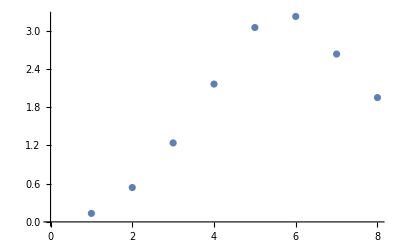

```mathematica
ListPlot[EXCITEFAC//Abs]
```

```mathematica
SimAmplitudes=Import["Values//only_amplitudes.txt"];
SimAmplitudes=StringReplace[SimAmplitudes,{"["->"","]"->""}];
SimAmplitudes="{"<>SimAmplitudes<>"}";
SimAmplitudes=ToExpression[SimAmplitudes];
allAmps=ToExpression/@SimAmplitudes;
allAmplitudes=Partition[allAmps,8];
```

```mathematica
SimPhase=Import["Values//only_phases.txt"];
SimPhase=StringReplace[SimPhase,{"["->"","]"->""}];
SimPhase="{"<>SimPhase<>"}";
SimPhase=ToExpression[SimPhase];
allPhi=ToExpression/@SimPhase;
allPhases=Partition[allPhi,8];
```

```mathematica
v=1;
theAMP=allAmplitudes[[v]]
thePHASE=allPhases[[v]]
```

{0.950766,3.92281,11.3876,26.8745,45.0171,45.2692,24.0949,5.29511}

{-0.669062,-1.7212,0.946635,0.895425,1.06572,-1.85511,1.48282,4.73956}

```mathematica
exciteCOEF=theAMP*Exp[I*thePHASE]
```

{0.745784-0.589713 ⅈ,-0.587798-3.87852 ⅈ,6.65513+9.24054 ⅈ,16.8016+20.9749 ⅈ,21.7827+39.3961 ⅈ,-12.698-43.4518 ⅈ,2.11697+24.0018 ⅈ,0.143854-5.29316 ⅈ}

```mathematica
SOURCEFAC=exciteCOEF/EXCITEFAC
```

{0.386522-7.12347 ⅈ,6.7961-2.61362 ⅈ,-0.652771-9.16824 ⅈ,8.54073+9.02827 ⅈ,-12.3932-8.02076 ⅈ,-11.9744-7.3395 ⅈ,-8.09411-4.26676 ⅈ,-2.64238-0.621205 ⅈ}

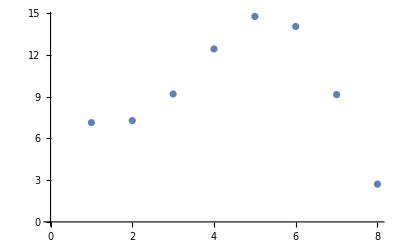

```mathematica
ListPlot[SOURCEFAC//Abs]
```

Now I want to sort the qnm freq just like how the spins were sorted, and bin the spins and frequencies and amplitudes and phases to respective amounts.

```mathematica
sortedAllω=List[];
sortedAllAmp=List[];
sortedAllϕ=List[];
For[i=1,i<=Length[spinsSorted],i++,
AppendTo[sortedAllω,allω[[Position[spins,spinsSorted[[i]]][[1,1]],1;;8]]];
AppendTo[sortedAllAmp,allAmplitudes[[Position[spins,spinsSorted[[i]]][[1,1]]]]];
AppendTo[sortedAllϕ,allPhases[[Position[spins,spinsSorted[[i]]][[1,1]]]]]]
```

```mathematica
spinSort=spinsSorted;
```

```mathematica
BinSpinSorted=List[];
BinFreqSorted=List[];
BinAmpsSorted=List[];
BinPhaseSorted=List[];
For[n=1,n<=10,n++,
spinBins=List[];
freqBins=List[];
ampBins=List[];
phaseBins=List[];
For[i=1,i<=Length[spinSort],i++,
If[0.65+0.01*(n-1)<=spinSort[[i]]<=0.65+0.01*n,
AppendTo[spinBins,spinSort[[i]]];
AppendTo[freqBins,sortedAllω[[i]]];
AppendTo[ampBins,sortedAllAmp[[i]]];
AppendTo[phaseBins,sortedAllϕ[[i]]]

,Continue]];
AppendTo[BinFreqSorted,freqBins];
AppendTo[BinSpinSorted,spinBins];
AppendTo[BinAmpsSorted,ampBins];
AppendTo[BinPhaseSorted,phaseBins]]
```

```mathematica
CheckNu=List[];
For[i=1,i<=21,i++,AppendTo[CheckNu,GiveNu[χ,allω[[1,i]]]]]
```

FindRoot::reged: The point {1.,0.00921152} is at the edge of the search region {0.,1.} in coordinate 1 and the computed search direction points outside the region.

FindRoot::reged: The point {1.,0.0181591} is at the edge of the search region {0.,1.} in coordinate 1 and the computed search direction points outside the region.

FindRoot::reged: The point {1.,0.00837826} is at the edge of the search region {0.,1.} in coordinate 1 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
CheckNu
```

{0.717577+0.417148 ⅈ,0.60135+0.472829 ⅈ,1.+0.00921152 ⅈ,1.+0.0181591 ⅈ,1.+0.00837826 ⅈ,1.+0.013866 ⅈ,1.+0.0116424 ⅈ,0.227553+0. ⅈ,0.365307+1. ⅈ,0.+0.0251436 ⅈ,0.402764+0. ⅈ,1.+0.288683 ⅈ,0.065812+0. ⅈ,0.+0.00353421 ⅈ,1.+0.10294 ⅈ,-6.77626×10^-21+0.00795952 ⅈ,4.76478×10^-9+1.24208×10^-8 ⅈ,1.+0.119274 ⅈ,1.+0.870444 ⅈ,0.00672903+1. ⅈ,1.+0.929326 ⅈ}

```mathematica
exciteFactors=List[];
For[i=1,i<=21,i++,AppendTo[exciteFactors,ExcitationFactorO[χ,allω[[1,i]],ωshift[allω[[1,i]]],GiveNu[χ,allω[[1,i]]],GiveNu[χ,ωshift[allω[[1,i]]]]]]]
```

FindRoot::reged: The point {1.,0.00921152} is at the edge of the search region {0.,1.} in coordinate 1 and the computed search direction points outside the region.

FindRoot::reged: The point {1.,0.00921163} is at the edge of the search region {0.,1.} in coordinate 1 and the computed search direction points outside the region.

FindRoot::reged: The point {1.,0.0181591} is at the edge of the search region {0.,1.} in coordinate 1 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
exciteFactors
```

{0.0882057+0.0999079 ⅈ,0.115852-0.526145 ⅈ,-0.00536874+0.00245265 ⅈ,-0.0839461-0.00665587 ⅈ,-0.00291618+0.00194045 ⅈ,0.329063-0.274281 ⅈ,0.0620954+0.44959 ⅈ,0.0131861+0.253128 ⅈ,253.922-19.0473 ⅈ,4.26627+1.50499 ⅈ,9.16996+3.86127 ⅈ,123.848-76.0158 ⅈ,6.10514-13.9291 ⅈ,0.733792-43.6508 ⅈ,-88.1417-219.321 ⅈ,-40.5317-89.3155 ⅈ,-0.0000749827-0.00239749 ⅈ,146.938+1325.33 ⅈ,-265576.+996728. ⅈ,508926.+2.53458×10^6 ⅈ,-3.68972×10^6-1.67837×10^6 ⅈ}

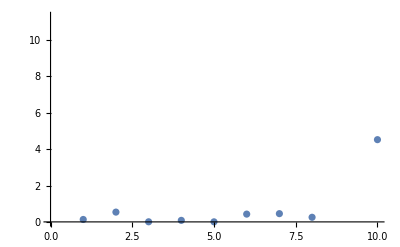

```mathematica
ListPlot[exciteFactors[[1;;10]]//Abs]
```

```mathematica
spins =Import["All_Spins.txt"];
spins=StringDelete[spins,"["];
spins=StringDelete[spins,"]"];
spins=StringInsert[spins,"{",1];
spins=StringInsert[spins,"}",-1];
spins=ToExpression[spins];
```

```mathematica
freq =Import["all_qnm_freq.txt"];
freq=StringDelete[freq,"["];
freq=StringDelete[freq,"]"];
freq=StringInsert[freq,"{",1];
freq=StringInsert[freq,"}",-1];
freq=ToExpression[freq];
allFreq=List[];
For[i=1,i<=Length[freq],i++,AppendTo[allFreq,ToExpression[freq[[i]]]]]
allω=List[];
For[i=1,i<=Length[allFreq]/21,i++,AppendTo[allω,allFreq[[21*(i-1)+1;;21*i]]]]
```

```mathematica
spinSort=spins//Sort;
```

```mathematica
sortedAllω=List[];
For[i=1,i<=Length[spinSort],i++,
AppendTo[sortedAllω,allω[[Position[spins,spinSort[[i]]][[1,1]]]]]]
```

```mathematica
allSpinSorted=List[];
allFreqSorted=List[];
For[n=1,n<=10,n++,
spinBins=List[];
freqBins=List[];
For[i=1,i<=Length[spinSort],i++,
If[0.65+0.01*(n-1)<=spinSort[[i]]<=0.65+0.01*n,AppendTo[spinBins,spinSort[[i]]];AppendTo[freqBins,sortedAllω[[i,1;;8]]],Continue]];
AppendTo[allFreqSorted,freqBins];
AppendTo[allSpinSorted,spinBins]]
```

```mathematica
allSpinSorted[[n]]//Length
```

100

```mathematica
χM
```

0.686184

```mathematica
NuSeed=Import["NuSeeds.mx"];
```

```mathematica
allFreqSorted[[1,4]]
```

{0.512053-0.0824554 ⅈ,0.499168-0.249559 ⅈ,0.475644-0.422092 ⅈ,0.445206-0.599701 ⅈ,0.413981-0.776862 ⅈ,0.395209-0.951688 ⅈ,0.391763-1.13736 ⅈ,0.391461-1.33578 ⅈ}

```mathematica
ShiftValue
```

1/1000000000

```mathematica
allNuSortedShifted=List[];
For[i=1,i<=Length[NuSeed],i++,
NewNu=List[];
νS=NuSeed[[i]];
For[n=1,n<=Length[allSpinSorted[[i]]],n++,
allν=List[];
χ=allSpinSorted[[i,n]];
omegas=allFreqSorted[[i,n]]+ShiftValue;
For[k=1,k<=Length[omegas],k++,
AppendTo[allν,GiveNu[χ,omegas[[k]],νS[[k]]]]];
AppendTo[NewNu,allν]
];
AppendTo[allNuSortedShifted,NewNu]]
```

```mathematica
allNuSortedShifted
```

{1}
 |  |  |  |

```mathematica
allNuSorted=List[];
For[i=1,i<=Length[NuSeed],i++,
NewNu=List[];
νS=NuSeed[[i]];
For[n=1,n<=Length[allSpinSorted[[i]]],n++,
allν=List[];
χ=allSpinSorted[[i,n]];
omegas=allFreqSorted[[i,n]];
For[k=1,k<=Length[omegas],k++,
AppendTo[allν,GiveNu[χ,omegas[[k]],νS[[k]]]]];
AppendTo[NewNu,allν]
];
AppendTo[allNuSorted,NewNu]
]
```

```mathematica
allNuSorted[[1,1,1]]
```

1.68872+0.355393 ⅈ

```mathematica
ν=allNuSorted[[1,1,1]]
νShift=allNuSortedShifted[[1,1,1]]
ω=allFreqSorted[[1,1,1]]
ωShift=allFreqSorted[[1,1,1]]+ShiftValue
χ=allSpinSorted[[1,1]]
```

1.68872+0.355393 ⅈ

1.68872+0.355393 ⅈ

0.511971-0.0824617 ⅈ

0.511971-0.0824617 ⅈ

0.650005

```mathematica
allExciteSorted=List[];
For[i=1,i<=Length[allSpinSorted],i++,
ExciteBins=List[];
For[n=1,n<=Length[allSpinSorted[[i]]],n++,
ExciteFactors=List[];
χ=allSpinSorted[[i,n]];
omegas=allFreqSorted[[i,n]];
omegasShift=allFreqSorted[[i,n]]+ShiftValue;
For[k=1,k<=Length[omegas],k++,
ν=allNuSorted[[i,n,k]];
νShift=allNuSortedShifted[[i,n,k]];
AppendTo[ExciteFactors,ExcitationFactorO[χ,omegas[[k]],omegasShift[[k]],ν,νShift]];
];
AppendTo[ExciteBins,ExciteFactors]
];
AppendTo[allExciteSorted,ExciteBins]
]
```

```mathematica
spinremoved=List[0.65472260966,
0.680979004173,
0.658332049514,
0.688028319113,
0.680197902659,
0.697209331299]
```

{0.654723,0.680979,0.658332,0.688028,0.680198,0.697209}

```mathematica
Position[allSpinSorted[[1]],Nearest[allSpinSorted[[1]],spinremoved[[1]]][[1]]][[1,1]]
```

23

```mathematica
0.654722609665
```

```mathematica
alist
```

{{1,2,3},{3,4,5}}

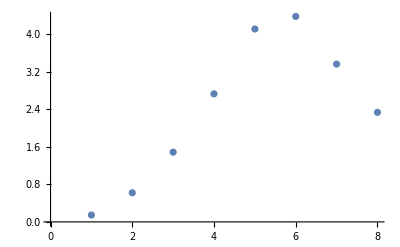

```mathematica
ListPlot[allExciteSorted[[1,1]]//Abs]
```

```mathematica
ExcitationFactorO[χ,ω,ωShift,ν,νShift]
```

0.119249+0.0416062 ⅈ

```mathematica
allNuSortedVals=Import["All_Nu_Sorted_Values.mx"];
```

```mathematica
allNuSortedVals//Length
```

10

```mathematica
SortedExciteFactors=Import["All_Sorted_ExcitationFactors.mx"]
```

{{{0.0902025+0.0867394 ⅈ,0.0535769-0.488917 ⅈ,4,-1.6894-1.56619 ⅈ,0.865512+1.54427 ⅈ},{1},49,{1},{1}},9}
 |  |  |  |

```mathematica
allExciteSorted
```

{1}
 |  |  |  |

```mathematica
SortedExciteFactors//Length
```

10

```mathematica
allSpinSorted//Length
```

10

```mathematica
allFreqSorted//Length
```

10

```mathematica
(0.686070803238+0.686297469599)/2
```

0.686184

```mathematica
spinremoved=List[0.65472260966,
0.680979004173,
0.658332049514,
0.688028319113,
0.680197902659,
0.697209331299]
```

{0.654723,0.680979,0.658332,0.688028,0.680198,0.697209}

```mathematica
firstExcite=SortedExciteFactors[[1]]//Length
firstSpins=allSpinSorted[[1]]//Length
firstFreqs=allFreqSorted[[1]]//Length
firstNu=allNuSortedVals[[1]]//Length
firstNuShift=allNuSortedShifted[[1]]//Length
```

53

53

53

«2 more identical outputs»

```mathematica
firstExcite=SortedExciteFactors[[1]];
firstSpins=allSpinSorted[[1]];
firstFreqs=allFreqSorted[[1]];
firstNu=allNuSortedVals[[1]];
firstNuShift=allNuSortedShifted[[1]];
For[i=1,i<=Length[spinremoved],i++,
pos=Position[firstSpins,Nearest[firstSpins,spinremoved[[i]]][[1]]][[1,1]];
firstSpins=Delete[firstSpins,pos];
firstExcite=Delete[firstExcite,pos];
firstFreqs=Delete[firstFreqs, pos];
firstNu=Delete[firstNu,pos];
firstNuShift=Delete[firstNuShift,pos];
]
```

```mathematica
firstExcite//Length
```

47

```mathematica
allSpinSorted=ReplacePart[allSpinSorted,1->firstSpins];
allFreqSorted=ReplacePart[allFreqSorted,1->firstFreqs];
SortedExciteFactors=ReplacePart[SortedExciteFactors,1->firstExcite];
allNuSortedVals=ReplacePart[allNuSortedVals,1->firstNu];
allNuSortedShifted=ReplacePart[allNuSortedShifted,1->firstNuShift];
```

```mathematica
allAmplitudesSorted=Import["All_Amplitudes_Sorted.mx"];
allPhasesSorted=Import["All_Phases_Sorted.mx"];
```

```mathematica
coefFactor=allAmplitudesSorted*Exp[I*allPhasesSorted]
```

{1}
 |  |  |  |

```mathematica
SortedSourceFactors=List[];
For[i=2,i<=Length[SortedExciteFactors],i++,
EFactors=List[];
For[j=1,j<=Length[SortedExciteFactors[[i]]],j++,
AppendTo[EFactors,coefFactor[[i,j]]/SortedExciteFactors[[i,j]]]];
AppendTo[SortedExciteFactors,EFactors]
]
```

Part::partw: Part 98 of {«1»} does not exist.

Part::partw: Part 99 of {«1»} does not exist.

Part::partw: Part 100 of {«1»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

$Aborted

```mathematica
allSpinSorted[[1]]//Length
```

47

{1}
 |  |  |  |

```mathematica
SortedExciteFactors//Length
```

10

```mathematica
coefFactor[[1]]//Length
```

51

```mathematica
SortedExciteFactors[[1]]//Length
```

53

```mathematica
allPhasesSorted[[1]]//Length
```

51

-2

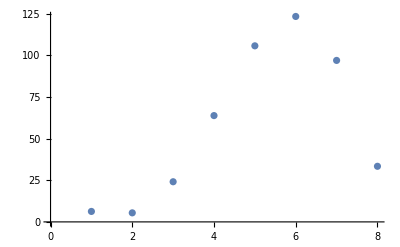

Thread::tdlen: Objects of unequal length in {«1»} {{5.75998-5.53884 ⅈ,0.221474+2.02107 ⅈ,-0.697075-0.580567 ⅈ,«3»,-0.318333+0.295117 ⅈ,0.276178-0.492766 ⅈ},{«1»},«7»,{«1»},«37»} cannot be combined.

Thread::tdlen: Objects of unequal length in {«1»} {«1»} cannot be combined.

Thread::tdlen: Objects of unequal length in {«1»,{0.949839+0.169758 ⅈ,2.85581-3.05238 ⅈ,3.96018-10.6189 ⅈ,«3»,14.2676-6.5563 ⅈ,-3.18643+0.849494 ⅈ},«7»,{0.604585-«19» ⅈ,«7»},«67»} «1» cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

{1}
 |  |  |  |

```mathematica
i=-2
ListPlot[(coefFactor[[9,i]]/SortedExciteFactors[[9,i]])//Abs]
```

```mathematica
coefFactor[[1,1]]
```

{0.735079+0.54787 ⅈ,0.794205+2.69643 ⅈ,13.6513-25.3318 ⅈ,88.5259-104.825 ⅈ,257.932-203.741 ⅈ,360.295-188.985 ⅈ,236.769-82.229 ⅈ,59.5235-15.0313 ⅈ}

```mathematica
allAmplitudesSorted[[1,1]]*Exp[I*allPhasesSorted[[1,1]]]
```

{0.735079+0.54787 ⅈ,0.794205+2.69643 ⅈ,13.6513-25.3318 ⅈ,88.5259-104.825 ⅈ,257.932-203.741 ⅈ,360.295-188.985 ⅈ,236.769-82.229 ⅈ,59.5235-15.0313 ⅈ}

```mathematica
sourceFactor = coefFactor/SortedExciteFactors[[-1,1]]
```

{-2.97523-6.01121 ⅈ,-5.18728+5.05503 ⅈ,-3.12715-7.62082 ⅈ,7.84524+4.51378 ⅈ,-8.06995-3.06658 ⅈ,-6.38085-3.33952 ⅈ,3.85979+2.38496 ⅈ,-1.26729-0.435893 ⅈ}

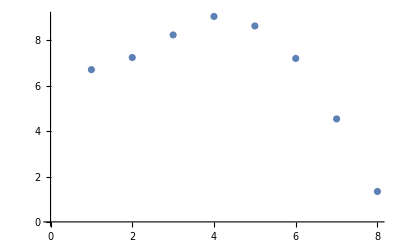

```mathematica
ListPlot[sourceFactor//Abs]
```

```mathematica
allPhasesSorted
```

{{},{},{},{},{},{},{},{},{},{}}